Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

V==-0.911325&&R==-0.159036

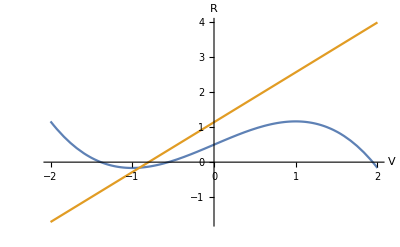

```mathematica
(* Задача 1 *)
Clear[V,R];
a=0.5;
b=0.8;
c=0.7;
d=3;
dVdt=V-V^3/d-R+a;
dRdt=V+b-c R;
Reduce[dVdt==0&&dRdt==0,{V,R},Reals]
equilibriumPoint={nV,nR}={-0.911325,-0.159036};
Vnull=V-V^3/d+a;
Rnull=(V+b)/c;
isoclinePlot=Plot[{Vnull,Rnull},{V,-2,2},AxesLabel->{"V","R"},AxesOrigin->{0,0}]
```

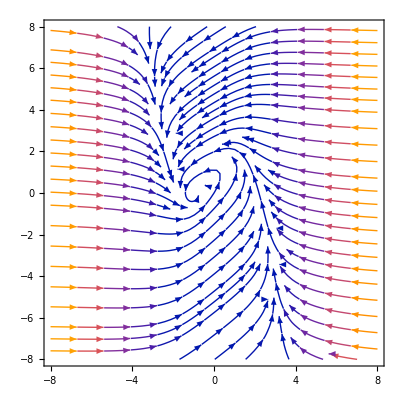

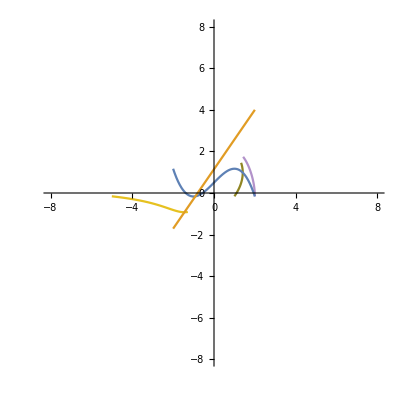

```mathematica
Clear[V,R];
T=20;
V01=2;
V02=-1;
V0={2,-1,-5,1};
sols=NDSolveValue[{V'[t]==V[t]-V[t]^3/d-R[t]+a,R'[t]==V[t]+b-c R[t],V[0]==#,R[0]==equilibriumPoint⟦2⟧},{V,R},{t,0,T}]&/@V0;
sol1Plot=ParametricPlot[{Vsol1[t],Rsol1[t]},{t,0,T},PlotRange->All,AxesOrigin->{0,0},PlotStyle->Red];
sol2Plot=ParametricPlot[{Vsol2[t],Rsol2[t]},{t,0,T},PlotRange->All,AxesOrigin->{0,0},PlotStyle->Green];
solPlots=ParametricPlot[Through[#[t]],{t,0,T},PlotRange->{{-8,8},{-8,8}},AxesOrigin->{0,0},PlotStyle->RandomColor[]]&/@sols;
streamPlot=StreamPlot[{dVdt,dRdt},{V,-8,8},{R,-8,8},AxesOrigin->{0,0}]
Show[{sol1Plot,sol2Plot,isoclinePlot}];
Show[Append[solPlots,isoclinePlot]]
Show[Join[solPlots,{isoclinePlot,streamPlot}]];
```

```mathematica
Clear[V,R];
X=1;
T=2;
V0={100};
diffusionSols=NDSolveValue[{
D[V[t,x], t]==200 D[V[t,x], x,x]+V[t,x]-V[t,x]^3/d-R[t,x]+a,
D[R[t,x], t]==0.01 D[R[t,x], x,x]+V[t,x]+b-c R[t,x],
V[0,x]==If[x<0.1X,#,nV],R[0,x]==nR,
V[t,0]==nV,V[t,X]==nV,
R[t,0]==nR,R[t,X]==nR
},
{V,R},{t,0,T},{x,0,X},AccuracyGoal->4,PrecisionGoal->4]&/@V0
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolveValue::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{InterpolatingFunction[{{0., 2.}, {0., 1.}}, <>],InterpolatingFunction[{{0., 2.}, {0., 1.}}, <>]}}

```mathematica
Manipulate[
Show[
Plot[#⟦1⟧[t,x],{x,0,X},PlotRange->{-5,100},AxesOrigin->{0,0},PlotStyle->Red]&/@diffusionSols
],{t,0,T}]
```

Show::gtype: Symbol is not a type of graphics.

```mathematica
diffV=0.5;
diffR=0.2;
T=15;
l=1;
Subscript[l, 1]=0.2;
h=0.1;
τ=h^2/(4diffV);
n=Ceiling[l/h];
m=Ceiling[T/τ];
mesh=Table[k h, {k, 0, n}];
u0={nV+3,nR};
f[{V_,R_}]:={V-V^3/d-R+a,V+b-c R}
sol=ConstantArray[{0,0},{m+1,n+1}];
sol⟦1⟧=Table[If[i h ≤ Subscript[l, 1],u0,equilibriumPoint],{i,0,n}];
```

```mathematica
For[j=1,j≤m,j++,
(*sol⟦j+1, 1⟧=(1-(2d τ)/h^2)sol⟦j, 1⟧+(2d τ)/h^2 sol⟦j,2⟧+τ f@sol⟦j, 1⟧;*)
sol⟦j+1, 1,1⟧=(1-(2diffV  τ)/h^2)sol⟦j, 1,1⟧+(2diffV  τ)/h^2 sol⟦j,2,1⟧+τ f[sol⟦j,1⟧]⟦1⟧;
(*sol⟦j+1, 1,1⟧=nV;*)
sol⟦j+1, 1,2⟧=nR;
For[i=2,i≤n,i++,
(*sol⟦j+1, i⟧=(d τ)/h^2(sol⟦j, i+1⟧+sol⟦j, i-1⟧)+(1-(2d τ)/h^2)sol⟦j, i⟧+τ f@sol⟦j, i⟧;*)
thisf=τ f@sol⟦j, i⟧;
sol⟦j+1, i,1⟧=(diffV τ)/h^2(sol⟦j, i+1,1⟧+sol⟦j, i-1,1⟧)+(1-(2diffV τ)/h^2)sol⟦j, i,1⟧+thisf⟦1⟧;
sol⟦j+1, i,2⟧=(diffR τ)/h^2(sol⟦j, i+1,2⟧+sol⟦j, i-1,2⟧)+(1-(2diffR τ)/h^2)sol⟦j, i,2⟧+thisf⟦2⟧;
];
(*sol⟦j+1, n+1⟧=(1-(2d τ)/h^2)sol⟦j, n+1⟧+(2d τ)/h^2 sol⟦j,n⟧+τ f@sol⟦j, n+1⟧;*)
(*sol⟦j+1, n+1,1⟧=(1-(2diffV  τ)/h^2)sol⟦j, n+1,1⟧+(2diffV  τ)/h^2 sol⟦j,n,1⟧+τ f[sol⟦j,n+1⟧]⟦1⟧;*)
sol⟦j+1, 1,1⟧=nV;
sol⟦j+1, n+1,2⟧=nR;
];
```

```mathematica
{Vsol,Rsol}=Table[sol⟦k,i,s⟧,{s,1,2},{k,1,m+1},{i,1,n+1}];
atMesh[sol_]:=Thread[{mesh,sol}];
```

```mathematica
Animate[
GraphicsGrid[{{
ListLinePlot[atMesh@Vsol⟦j⟧,PlotStyle->Red,PlotRange->{-5,5}, PlotLabel->"S"],
ListLinePlot[atMesh@Rsol⟦j⟧,PlotStyle->Red,PlotRange->{-1,1}, PlotLabel->"B"]
}}]
,{j,1,m +1,1},DisplayAllSteps->True,AnimationRate->3,AnimationRunning->False
]
```